```mathematica
death=Flatten[Import[NotebookDirectory[]<>"ZUMA1_PFS_death.dat"],0]
L=death//Length
avMonth=(7 31+28+4*30)/12.
e=Join[{{0,1}},{death⟦#,1⟧avMonth,death⟦#,2⟧1./100.}&/@Range[1,L,1]]
```

{{0.178164,99.0835},{0.340132,98.3502},{0.534493,97.2505},{0.566887,96.1515},{0.728854,94.3193},{1.0204,93.2192},{1.16617,92.1197},{1.36053,90.8368},{1.4901,90.2868},{1.66827,89.1872},{1.71686,88.2712},{1.76545,87.3553},{1.84643,86.4392},{1.92741,84.4242},{2.10558,83.5077},{2.23515,82.5914},{2.31614,81.1259},{2.41332,80.2097},{2.44571,79.477},{2.57528,78.5607},{2.67247,77.8277},{2.75345,76.3622},{2.80204,74.5304},{2.81824,71.4168},{2.86683,70.5009},{2.9802,69.4015},{2.9964,66.471},{3.02879,65.1888},{3.09358,61.1593},{3.27175,60.4259},{3.35273,59.5098},{3.75765,58.4092},{4.43791,57.6738},{4.47031,56.3916},{4.81044,55.4745},{5.13437,54.3742},{5.57169,52.5409},{5.65267,51.4416},{5.84703,50.3419},{5.92801,49.2427},{6.08998,47.4105},{7.28854,46.3066},{9.07019,45.5666},{9.21596,44.4671},{11.9694,43.9062},{12.4877,42.0725},{24.3761,42.023}}

47

30.4167

{{0,1},{5.41917,0.990835},{10.3457,0.983502},{16.2575,0.972505},{17.2428,0.961515},{22.1693,0.943193},{31.037,0.932192},{35.4709,0.921197},{41.3827,0.908368},{45.3239,0.902868},{50.7431,0.891872},{52.2211,0.882712},{53.699,0.873553},{56.1623,0.864392},{58.6255,0.844242},{64.0447,0.835077},{67.9859,0.825914},{70.4492,0.811259},{73.4051,0.802097},{74.3904,0.79477},{78.3316,0.785607},{81.2875,0.778277},{83.7507,0.763622},{85.2287,0.745304},{85.7214,0.714168},{87.1993,0.705009},{90.6479,0.694015},{91.1405,0.66471},{92.1258,0.651888},{94.0964,0.611593},{99.5156,0.604259},{101.979,0.595098},{114.295,0.584092},{134.987,0.576738},{135.972,0.563916},{146.317,0.554745},{156.171,0.543742},{169.472,0.525409},{171.935,0.514416},{177.847,0.503419},{180.31,0.492427},{185.237,0.474105},{221.693,0.463066},{275.885,0.455666},{280.319,0.444671},{364.069,0.439062},{379.834,0.420725},{741.44,0.42023}}

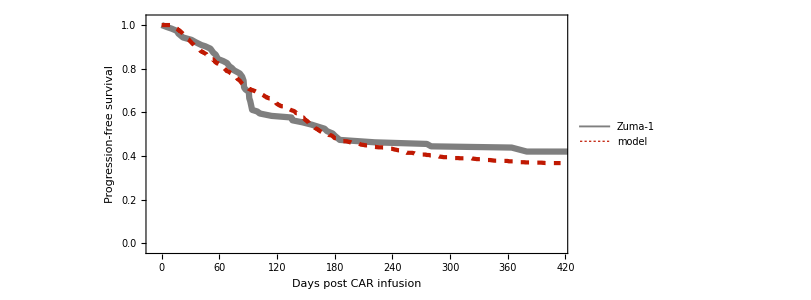

```mathematica
Tf=415;

LPsim=ListPlot[(*{rB1[x],rB2[x],rB3[x]},{x,0,Tf},*)
{
e,
{#,rBsurvivalCurves[[5]][#]}&/@Range[0,Tf,Tf/1000.]
},
Joined->{True,True},
PlotRange->{{-0.02,1.05}Tf 0.95,{-0.025,1.025}},
PlotLegends->Placed[{"Zuma-1","model","simulation 2"},{0.85,0.75}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->{
{Thickness[0.0075],Opacity[0.5,Black]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.2]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.6]}
}
]
```